# Cosmomathica

Adrian Vollmer, Institute for theoretical Physics, Universität Heidelberg, 2014

This notebook demonstrates how to use the Cosmomathica package version 0.3.

## Calling external programs

### Initialization

First, load the Cosmomathica package

```mathematica
<<(NotebookDirectory[]<>"cosmomathica.m")
```

A short description for all functions

```mathematica
?Transfer
```

Transfer[OmegaM, fBaryon, Tcmb, h] provides an interface to Eisenstein & Hu's fitting formula for the transfer function (high baryon case). It takes the total matter density Ω_M, the fraction of baryons Ω_b/Ω_M, the CMB temperature and the dimensionless Hubble constant h as input, and returns the sound horizon, the wavenumber k_peak where the spectrum has a maximum, the transfer function for CDM, baryons, both, or with no baryons or no wiggles.

```mathematica
?TFPower
```

TFPower[OmegaM, OmegaB, OmegaMN, DegenNu, OmegaL, h, z] provides an interface to Eisenstein & Hu's fitting formula for the transfer function (mixed matter case). It takes the total matter density Ω_M, the baryon density Ω_b, the massive neutrino density Ω_ν, the integer number of degenerate massive neutrino species, the dark energy density Ω_L, the dimensionless Hubble constant h, and the redshift z as input, and return the transfer function at the given redshift.

```mathematica
?Halofit
```

Halofit[OmegaM, OmegaL, gammaShape, sigma8, ns, betaP, z0] provides an interface to the halofit algorithm by Robert E. Smith et al. (reimplemented in C by Martin Kilbinger). It takes the total matter density Ω_M, the vacuum energy density Ω_L, a shape factor, σ_8, n_s, β_p, and a fixed redshift z_0 as input, and returns the nonlinear matter power spectrum (computed in three ways: linearly with the BBKS alogorithm, nonlinear with the algorithm by Peacock and Dobbs, or nonlinearly with the Halofit algorithm) at 20 different values of the scale factor and the convergence power spectrum in tabulated form.

```mathematica
?CosmicEmu
```

CosmicEmu[omegaM, omegaB, sigma8, ns, w] provides an interface to the CosmicEmulator by Earl Lawrence. It takes ω_M, ω_b, σ_8, n_s, and the equation of state w, and returns the nonlinear matter power spectrum at five different redshifts as well as z, H, d (all at last scattering), and the sound horizon.

```mathematica
?FrankenEmu
```

FrankenEmu[omegaM, omegaB, h, sigma8, ns, w] provides an interface to FrankenEmu by Earl Lawrence. It takes ω_M, ω_b, h, σ_8, n_s, and the equation of state w, and returns the nonlinear matter power spectrum at five different redshifts as well as z, H, d (all at last scattering), and the sound horizon. The Hubble parameter h can also be omitted, in which case it will be determined from the CMB just as in CosmicEmu. Additional cosmological parameters are only returned if h is missing.

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, OmegaL, h, w] provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

```mathematica
?Copter
```

Copter[OmegaM, OmegaB, h, ns, sigma8, transfer, z, type] provides an interface to Copter by Jordan Carlson. It takes Ω_M, Ω_b, h, n_s, σ_8, the transfer function in shape of a list of value pairs and returns the power spectrum and other quantities. The 'type' variable specifies which pertubration theory is used and must take one of the following values (as a string): 'SPT' (Standard PT), 'RPT' (Renormalized PT), 'LPT' (Lagrangian PT), 'FWT' (Flowing with time, TRG), 'LargeN', 'HSPT' (Higher order PT), 'NW' (no wiggles, Eisenstein&Hu algorithm), 'Linear'. Several options can be specified.

```mathematica
?Class
```

Class["parameter1" -> "value1",...] runs Class. You need to specifiy all Class parameters in the form of options. Cosmomathica then writes all options into an ini-file, where each line contains "parameter = value". This file is fed to Class and the output is returned.

```mathematica
NotebookDirectory[]
```

/home/santiago/CosmoProjects/cosmomathica-cambtest/

### Transfer

This is how you call Eisenstein&Hu’s Transfer function code

```mathematica
tfdata=Transfer[.12,.3,2.7,.67];
```

To see what kind of data has been returned, type this

```mathematica
tfdata[[All,1]]
```

{Transfer[soundhorizon],Transfer[peak],Transfer[kvalues],Transfer[full],Transfer[baryon],Transfer[cdm],Transfer[nowiggles],Transfer[zerobaryons]}

To access it, use the replacement rules, e.g. for the sound horizon

```mathematica
Transfer["soundhorizon"]/.tfdata
```

128.773

or for the various transfer functions

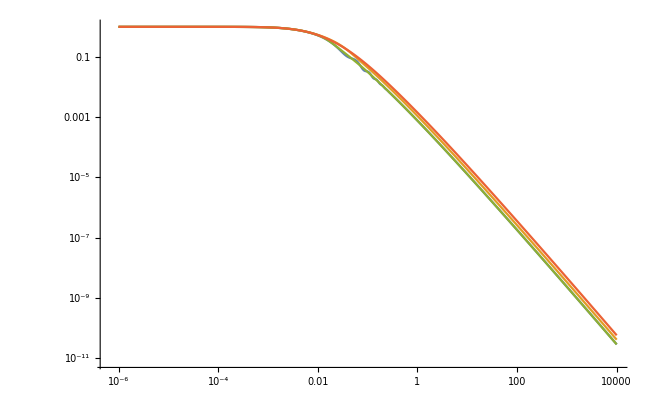

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Transfer["kvalues"]/.tfdata,pk}],{pk,{
Transfer["full"],
Transfer["cdm"],
Transfer["nowiggles"],
Transfer["zerobaryons"]
}/.tfdata}],Joined->True]
```

The mixed matter case is a bit simpler :

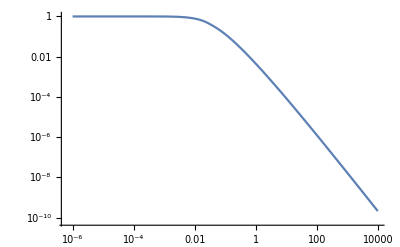

```mathematica
ListLogLogPlot[TFPower[.3,.05,0,0,.7,.7,0.],Joined->True]
```

### Halofit

Call the Halofit+ code

```mathematica
hfdata=Halofit[.25,.75,.259,.8,.9,1.,1.5];
```

View the output data options

```mathematica
hfdata[[All,1]]
```

{Halofit[avalues],Halofit[kvalues],Halofit[ellvalues],Halofit[kappaBBKS],Halofit[BBKS],Halofit[kappaPD96],Halofit[PD96],Halofit[kappaHalofit],Halofit[Halofit]}

Plot the matter power spectrum using the Halofit algorithm at different redshifts

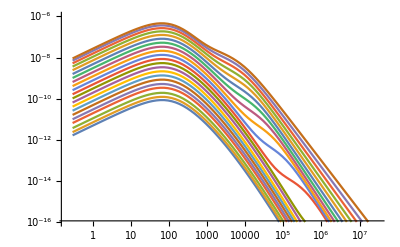

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Halofit["kvalues"]/.hfdata,pk}],
{pk,Halofit["Halofit"]/.hfdata}],
Joined->True,PlotRange->{1*^-16,1*^-6}]
```

Note that Halofit[“Halofit”] returns a list of lists, each of which corresponds to the power spectrum at a different redshift or scale factor. The scale factors are as follows

```mathematica
Halofit["avalues"]/.hfdata
```

{0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.}

Plot the convergence power spectrum using three different algorithms

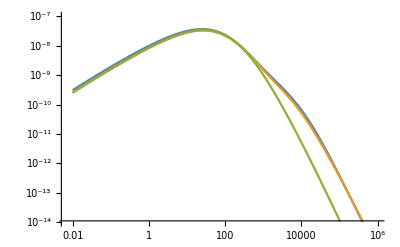

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose[{Halofit["ellvalues"]/.hfdata,kappa}],{kappa,{
Halofit["kappaHalofit"],
Halofit["kappaPD96"],
Halofit["kappaBBKS"]
}/.hfdata}],Joined->True,PlotRange->{1*^-14,1*^-7}]
```

### Cosmic Emulator

Call the Cosmic Emulator

```mathematica
cedata=CosmicEmu[.15,.022,.8,.9,-1];
```

View the output

```mathematica
cedata[[All,1]]
```

{CosmicEmu[zvalues],CosmicEmu[pk],CosmicEmu[soundhorizon],CosmicEmu[zlss],CosmicEmu[dlss],CosmicEmu[hubblecmb]}

Redshift of last scattering

```mathematica
CosmicEmu["zlss"]/.cedata
```

1093.05

Power spectrum at the following redshifts

```mathematica
CosmicEmu["zvalues"]/.cedata
```

{1.,0.666667,0.428571,0.25,0.111111,0.}

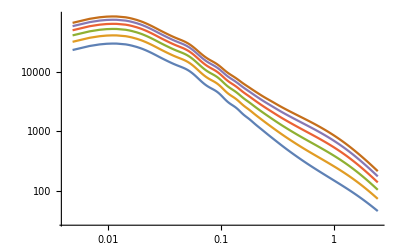

```mathematica
ListLogLogPlot[Evaluate@Table[pk,{pk,CosmicEmu["pk"]/.cedata}],Joined->True]
```

### FrankenEmu

Call FrankenEmu

```mathematica
fedata=FrankenEmu[.15,.022,.7,.85,.9,-1];
```

View the output

```mathematica
fedata[[All,1]]
```

{FrankenEmu[zvalues],FrankenEmu[pk]}

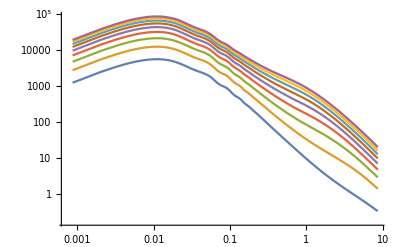

```mathematica
ListLogLogPlot[Evaluate@Table[pk,{pk,FrankenEmu["pk"]/.fedata}],Joined->True]
```

### CAMB

CAMB takes a lot of parameters. In Cosmomathica, most of them are being treated as options with default values while some of them are regular parameters that have to be specified. The distinction is arbitrary. These are the default options (see the CAMB documentation for details):

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, OmegaL, h, w] provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

```mathematica
Options[CAMB]
```

{Tcmb→2.7255,OmegaNu→0,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→none,WantCMB→True,WantTransfer→True,WantCls→True,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,TransferHighPrecision→False,WantScalars→True,WantVectors→True,WantTensors→True,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→3000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→0.9,TransferKperLogInt→0,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→True,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best}

Run the CAMB code (without lensing the scalar angular power spectrum will contain only three curves corresponding to C_TT, C_EE, C_TE - see the CAMB documentation for further information) with the transfer function for two different redshifts

```mathematica
CAMB[.2,.05,.75,.67,-1.]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject['/home/santiago/CosmoProjects/cosmomathica-cambtest/ext/math_link',2216,5].

Interface::LinkBroken: CAMB crashed. See if there is anything useful on stdout.

$Aborted

```mathematica
cambdata=CAMB[.2,.05,.75,.67,-1.,WantTransfer->True,DoLensing->False,TransferRedshifts->{1.5,0.}];
```

LinkObject::linkd: Unable to communicate with closed link LinkObject['/home/santiago/CosmoProjects/cosmomathica-cambtest/ext/math_link',2239,5].

Interface::LinkBroken: CAMB crashed. See if there is anything useful on stdout.

$Aborted

```mathematica
cambdata[[All,1]]
```

{CAMB[age],CAMB[zstar],CAMB[rstar],CAMB[100thetastar],CAMB[zdrag],CAMB[rdrag],CAMB[kD],CAMB[100thetaD],CAMB[zEQ],CAMB[100thetaEQ],CAMB[sigma8],CAMB[CLscalar],CAMB[CLvector],CAMB[CLtensor],CAMB[redshifts],CAMB[PSlinear],CAMB[PSnonlinear],CAMB[Transfer]}

```mathematica
cambdata[[1]]
```

CAMB[age]→14.7873

Age of the universe:

```mathematica
CAMB["age"]/.cambdata
```

14.7873

There is a σ_8 for each redshift and for each spectral index

```mathematica
CAMB["sigma8"]/.cambdata
```

{{0.35308},{0.680405}}

Plot the scalar angular power spectrum

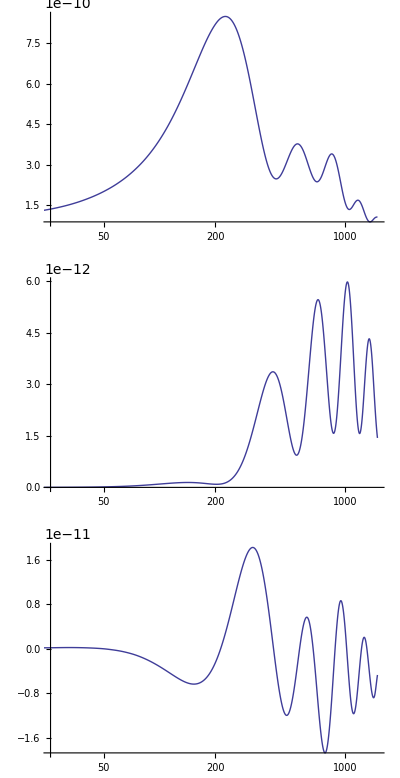

```mathematica
GraphicsGrid@Transpose@List@Table[ListLogLinearPlot[plot,Joined->True,PlotRange->All],{plot,CAMB["CLscalar"]/.cambdata}]
```

In version Nov13, CAMB computes the power spectrum at more than just the requested redshifts :

```mathematica
CAMB["redshifts"]/.cambdata
```

{9.,8.,7.,6.,5.,4.,3.,2.,1.5,1.,0.}

The results for the linear/nonlinear power spectrum as well as the transfer function contain a list for each redshift. Each one of those is a list of number pairs {k_i,P(k_i)} in the case of the power spectrum, and a list of seven numbers {k_i,T_1(k_i),..., T_6(k_i)} in case of the transfer function, each of which correspond to CDM, baryon, photon, massless neutrino, massive neutrinos, and total (massive).

Plot the nonlinear matter power spectrum for all redshifts

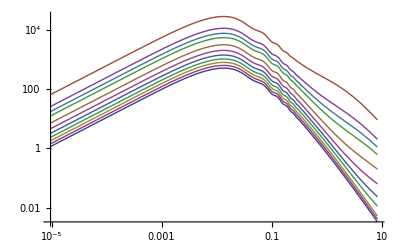

```mathematica
ListLogLogPlot[CAMB["PSnonlinear"]/.cambdata,Joined->True]
```

Plot the CDM transfer function at the first redshift

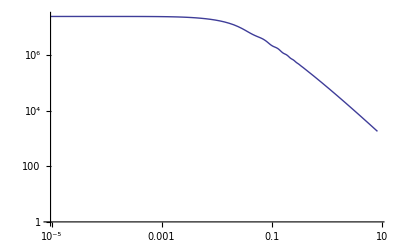

```mathematica
ListLogLogPlot[(CAMB["Transfer"]/.cambdata)[[-1,All,{1,2}]],Joined->True]
```

### Copter

There are some options to the Copter function that influence precision and speed (see Copter source code for details):

```mathematica
(*Options[Copter]*)
```

Call Copter (needs the transfer function from above)

```mathematica
(*copdata=Copter[.25,.05,.7,.9,.8,Transpose[{Transfer["kvalues"],Transfer["full"]}/.tfdata],0,"SPT"];*)
```

View the output

```mathematica
(*copdata[[All,1]]*)
```

```mathematica
(*ListLogLogPlot[{Transpose[{Copter["kvalues"],Copter["P11"]}/.copdata],
Transpose[{Copter["kvalues"],Copter["P12"]}/.copdata],
Transpose[{Copter["kvalues"],Copter["P22"]}/.copdata]},Joined->True]*)
```

The growth function can be computed with a separate function

```mathematica
(*zrange=Range[0,50,.1];
copgrowth=CopterGrowth[.25,.05,.7,.9,zrange];
ListLogPlot[Transpose[{zrange,copgrowth}],Joined->True]*)
```

## Class

Every parameter is configured by options. We build a .ini file from them and pass it on to Class. So every option of the form “key”->”value” becomes one line in the .ini file of the form “key = value”. Note that all values need to be strings. For details, read the file explanatory.ini which comes with the Class package.

```mathematica
classdata=Class["h" -> ".6","Omega_k"->"0.","n_s"->".9", "Omega_b"->"0.05",
"output"->"mTk,mPk",
"z_pk"->"0,1,2",
"gauge"->"synchronous"(*"newton"*),
"non linear"->"",
"P_k_max_h/Mpc"->"10",
"modes"->"s",
"format"->"camb"];
```

View the output

```mathematica
classdata[[All,1]]
```

{Class[kvalues],Class[tauvalues],Class[sigma8],Class[transfer],Class[PSlinear],Class[background]}

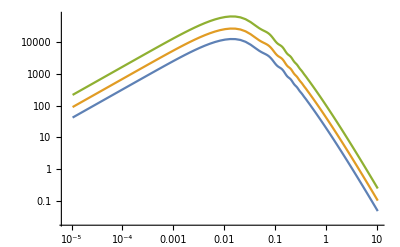

```mathematica
ListLogLogPlot[Evaluate@Table[Transpose@{Class["kvalues"]/.classdata,(Class["PSlinear"]/.classdata)[[i]]},{i,{1,5,10}}],Joined->True]
```

```mathematica
Directory[]
```

/home/santiago

## CAMB Tests

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/santiago/CosmoProjects/cosmomathica-cambtest

```mathematica
Options[CAMB]
```

{Tcmb→2.7255,OmegaNu→0,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→none,WantCMB→True,WantTransfer→True,WantCls→True,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,TransferHighPrecision→False,WantScalars→True,WantVectors→True,WantTensors→True,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→3000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→0.9,TransferKperLogInt→0,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→True,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best}

```mathematica
OptionValue[CAMB,#]&/@{OmegaNu,Tcmb,YHe,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions,ScalarSpectralIndex,ScalarRunning,TensorSpectralIndex,RatioScalarTensorAmplitudes,ScalarPowerAmplitude,PivotScalar,PivotTensor,OpticalDepth,ReionizationRedshift,ReionizationFraction,ReionizationDeltaRedshift,MaxEtaK,MaxEtaKTensor,TransferKmax}
```

{0,2.7255,0.24,3.046,{0},{1},{0.96},{0},{0},{1},{2.1×10^-9},0.05,0.05,0.,10.,1.,0.5,3000.,800.,0.9}

```mathematica
Reverse@Sort@OptionValue[CAMB,TransferRedshifts]
```

{0.}

```mathematica
initialcond={"vector","adiabatic","iso_CDM","iso_baryon","iso_neutrino","iso_neutrino_vel"};
nonlinear={"none","pk","lens","both"};
massivenu={"int","trunc","approx","best"};
```

```mathematica
bool2int[b_]:=If[b,1,0];
```

```mathematica
floats=Flatten@{0.2,0.05,0.75,0.67*100,OptionValue[CAMB,#]&/@{OmegaNu,Tcmb,YHe,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions,ScalarSpectralIndex,ScalarRunning,TensorSpectralIndex,RatioScalarTensorAmplitudes,ScalarPowerAmplitude,PivotScalar,PivotTensor,OpticalDepth,ReionizationRedshift,ReionizationFraction,ReionizationDeltaRedshift,MaxEtaK,MaxEtaKTensor,TransferKmax},Reverse@Sort@OptionValue[CAMB,#]&@TransferRedshifts}
```

{0.2,0.05,0.75,67.,0,2.7255,0.24,3.046,0,1,0.96,0,0,1,2.1×10^-9,0.05,0.05,0.,10.,1.,0.5,3000.,800.,0.9,0.}

```mathematica
ints=Flatten@{OptionValue[CAMB,MassiveNeutrinos],Length@OptionValue[CAMB,NuMassFractions],Position[initialcond,OptionValue[CAMB,ScalarInitialCondition]][[1,1]]-1,Position[nonlinear,OptionValue[CAMB,NonLinear]][[1,1]]-1,Length@OptionValue[CAMB,#]&@ScalarSpectralIndex,bool2int/@OptionValue[CAMB,#]&@{DoReionization,UseOpticalDepth,TransferHighPrecision,WantCMB,WantTransfer,WantCls,WantScalars,WantVectors,WantTensors,WantZstar, WantZdrag},OptionValue[CAMB,#]&/@{OutputNormalization,MaxEll,MaxEllTensor,TransferKperLogInt},Length@OptionValue[CAMB,#]&@TransferRedshifts,bool2int/@OptionValue[CAMB,#]&@{AccuratePolarization,AccurateReionization,AccurateBB,DoLensing,OnlyTransfers,DerivedParameters},Position[massivenu,OptionValue[CAMB,MassiveNuMethod]][[1,1]]-1}
```

{0,1,1,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1500,400,0,1,1,0,0,1,0,1,3}

```mathematica
Directory[]
```

/home/santiago/CosmoProjects/cosmomathica-cambtest

```mathematica
NotebookDirectory[]
```

/home/santiago/CosmoProjects/cosmomathica-cambtest/

```mathematica
SetDirectory[Directory[]<>"/ext/camb/"]
```

/home/santiago/CosmoProjects/cosmomathica-cambtest/ext/camb

```mathematica
link=Install[NotebookDirectory[]<>"/ext/math_link"];
```

```mathematica
CAMBrun[N/@floats, ints]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject['/home/santiago/CosmoProjects/cosmomathica-cambtest//ext/math_link',4064,6].

$Failed

```mathematica
Uninstall[link]
```

LinkObject::linkn: Argument LinkObject['/home/santiago/CosmoProjects/cosmomathica//ext/math_link',6089,7] in LinkClose[LinkObject['/home/santiago/CosmoProjects/cosmomathica//ext/math_link',6089,7]] has an invalid LinkObject number; the link may be closed.

'/home/santiago/CosmoProjects/cosmomathica//ext/math_link'

```mathematica
ResetDirectory[]
```

/home/santiago/CosmoProjects/cosmomathica